# RK Implementation

RK schemes for autonomous ODEs are defined by the Butcher matrix A and one or two b vectors. Fixed step size schemes have one vector b and variable step-size schemes have two vectors b_high which advances the scheme and b_low that is used to estimate error and choose the step size

### Fixed Step Size.

1+z+z^2/2+z^3/6+z^4/24

1+z+z^2/2+z^3/6+z^4/24

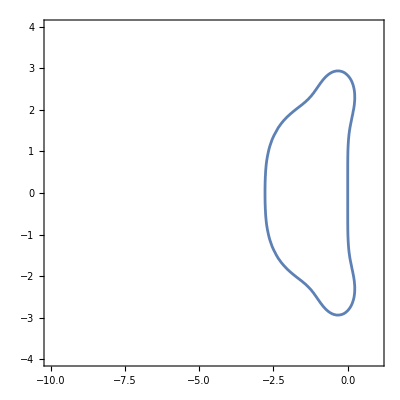

1+h (λ/6+1/3 λ (1+(h λ)/2)+1/3 λ (1+1/2 h λ (1+(h λ)/2))+1/6 λ (1+h λ (1+1/2 h λ (1+(h λ)/2))))

```mathematica
Clear[f,λ]
f[y_]:= λ y
ClassicRK4={({{0, 0, 0, 0}, {1/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, 1, 0}}),{1/6,1/3,1/3,1/6}};
ThreeEightRule={({{0, 0, 0, 0}, {1/3, 0, 0, 0}, {-1/3, 1, 0, 0}, {1, -1, 1, 0}}),{1/8,3/8,3/8,1/8}};
pRK4[z_]=Simplify[ExplicitRKFixedhStep[f,ClassicRK4,h][{t,y}]⟦2⟧/y]/.λ->z/h
pRK38[z_]=Simplify[ExplicitRKFixedhStep[f,ThreeEightRule,h][{t,y}]⟦2⟧/y]/.λ->z/h
ContourPlot[ Abs[pRK4[x + I y]]==1,{x, -10,1},{y,-4,4}]
ExplicitRKFixedhStep[f,ClassicRK4,h][{0,1}]⟦2⟧
```

```mathematica
Series[E^(λ h)-ExplicitRKFixedhStep[f,ClassicRK4,h][{0,1}]⟦2⟧,{h,0,5}]
Series[E^(λ h)-ExplicitRKFixedhStep[f,ThreeEightRule,h][{0,1}]⟦2⟧,{h,0,5}]
```

(λ^5 h^5)/120+O[h]^6

(λ^5 h^5)/120+O[h]^6

```mathematica
Clear[f,y,h,y0]
Simplify[
Series[y[h]-ExplicitRKFixedhStep[f,ThreeEightRule,h][{0,y[0]}]⟦2⟧,{h,0,5}]/.{
y'[0]->f[y[0]],
y''[0]->f'[y[0]]f[y[0]],
y'''[0]->f''[y[0]] f[y[0]]^2+f'[y[0]]^2 f[y[0]]}
]
```

```mathematica
Sub={
y'[t]->f[y[t]],
y''[t]->f[y[t]] f'[y[t]]
}
D[f[y[t]],t]/.Sub
```

{y'[t]→f[y[t]]}

f[y[t]] f'[y[t]]

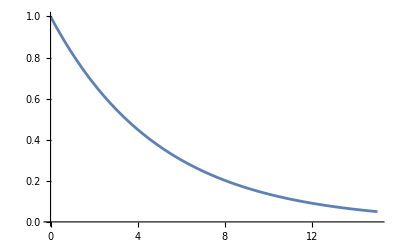

```mathematica
Plot[E^(-0.2 t),{t, 0, 15}]
```

```mathematica
ExplicitRKFixedhStep[f_,{A_,b_},h_][{t_,y_}]:= Module[{k,s=Length[b],yNew},
k[1]=f[y];
Do[
k[i]=f[y+h Sum[A⟦i,j⟧ k[j],{j,1,i-1}]],
{i,2,s}];
yNew=y+h Sum[b⟦i⟧ k[i],{i,1,s}];
{t+h, yNew}
]
```

The original RK schemes were fixed step size.

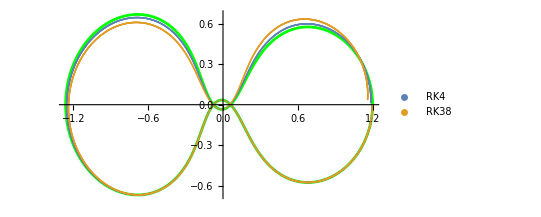

```mathematica
ClassicRK4={({{0, 0, 0, 0}, {1/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, 1, 0}}),{1/6,1/3,1/3,1/6}};
ThreeEightRule={({{0, 0, 0, 0}, {1/3, 0, 0, 0}, {-1/3, 1, 0, 0}, {1, -1, 1, 0}}),{1/8,3/8,3/8,1/8}};
DormandOrbit[{x_,y_,vx_,vy_}]:= Module[{μ=1/82.45,de,dm},
(*p163 Dormand *)
de=√((x+μ)^2+y^2); dm=√((x-1+μ)^2+y^2);
{vx,vy,
   2 vy +x-(1-μ) (x+μ)/de^3-μ (x-1+μ)/dm^3,
-2 vx +y-(1-μ) y/de^3-μ y/dm^3}]

y0={1.2,0,0,-1.049357509830320};
t0=0; TMax=6.192169331319640;
n=3000;
h=TMax/n;
ySol=NDSolveValue[{y'[t]==DormandOrbit[y[t]],y[0]==y0},y,{t,0, TMax}];
MmaPic=ParametricPlot[ySol[t]⟦{1,2}⟧,{t,0, TMax},PlotStyle->Green];
RK4CData=NestList[ExplicitRKFixedhStep[DormandOrbit,ClassicRK4,h],{t0,y0},n];
RK38Data=NestList[ExplicitRKFixedhStep[DormandOrbit,ThreeEightRule,h],{t0,y0},n];
Show[MmaPic,
ListPlot[{RK4CData⟦All,2,{1,2}⟧,RK38Data⟦All,2,{1,2}⟧},
PlotLegends->{"RK4","RK38"}]]
```

### Variable Step Size.

Adaptive step size with local error control was a huge improvement

```mathematica
ExplicitRKAdaptiveStep[f_,{A_,bHigh_,bLow_,LowOrder_},AbsTol_][{t_,y_,h_}]:= Module[{k,s=Length[bHigh],yHigh,yLow,Err,γ=0.9,α},
k[1]=f[y];
Do[
k[i]=f[y+h Sum[A⟦i,j⟧ k[j],{j,1,i-1}]],
{i,2,s}];
yHigh=y+h Sum[bHigh⟦i⟧ k[i],{i,1,s}];
yLow=y+h Sum[bLow⟦i⟧ k[i],{i,1,s}];
(* Error ≈||yHigh-yLow||=C h^(LowOrder+1)*)
Err=Norm[yHigh-yLow];
α=γ (AbsTol/Err)^(1/(LowOrder+1));
(* if Err = C h^(p+1) then C(α h)^(p+1)= AbsTol if α = (AbsTol/Err)^(1/(p+1)) *)
(* γ (frequently 0.9) is a safety factor. *)
(* If Err < AbsTol take step and estimate how big the next step can be *)
(* If Err > AbsTol skip step and try again with a smaller step *)
If[ Err<AbsTol,
{t+h, yHigh,α h },
{t, y,α h }]
]
```

The original RKF45 adaptive scheme is

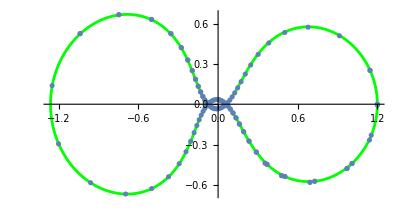

7.39549

```mathematica
RKF45={({{0, 0, 0, 0, 0, 0}, {1/4, 0, 0, 0, 0, 0}, {3/32, 9/32, 0, 0, 0, 0}, {1932/2197, -7200/2197, 7296/2197, 0, 0, 0}, {439/216, -8, 3680/513, -845/4104, 0, 0}, {-8/27, 2, -3544/2565, 1859/4104, -11/40, 0}}),
{16/135,0,6656/12825,28561/56430,-9/50,2/55},
{25/216,0,1408/2565,2197/4104,-1/5,0},4};
DormandOrbit[{x_,y_,vx_,vy_}]:= Module[{μ=1/82.45,de,dm},
(*p163 Dormand *)
de=√((x+μ)^2+y^2); dm=√((x-1+μ)^2+y^2);
{vx,vy,
   2 vy +x-(1-μ) (x+μ)/de^3-μ (x-1+μ)/dm^3,
-2 vx +y-(1-μ) y/de^3-μ y/dm^3}]

y0={1.2,0,0,-1.049357509830320};
t0=0; TMax=6.192169331319640; h0=1.2;
ySol=NDSolveValue[{y'[t]==DormandOrbit[y[t]],y[0]==y0},y,{t,0, TMax}];
MmaPic=ParametricPlot[ySol[t]⟦{1,2}⟧,{t,0,TMax},PlotStyle->Green];
RKF45Data=NestList[ExplicitRKAdaptiveStep[DormandOrbit,RKF45,10^-4],{t0,y0,h0},120];
Show[MmaPic, ListPlot[ RKF45Data⟦All,2,{1,2}⟧],PlotRange->All]
hs=RKF45Data⟦All,3⟧;
ts=RKF45Data⟦All,1⟧; ts⟦-1⟧
```

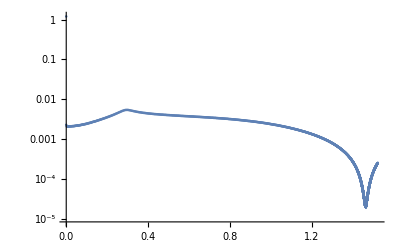

```mathematica
ListLogPlot[{ts,hs}ᵀ]
```